## Computing p(χ_eff = 0) Maria Okounkova

```mathematica
First let's compute p(Subscript[χ, eff]| q, ℳ) = 0
```

#### χ_eff in terms of {q, ℳ}

```mathematica
Solutionm1m2 = Solve[((m1*m2)^(3/5) / (m1 + m2)^(1/5))== ℳ  &&  m1/m2 == q,{m1,m2}]
```

{{m1→q^(2/5) (1+q)^(1/5) ℳ,m2→((1+q)^(1/5) ℳ)/q^(3/5)},{m1→-(-1)^(1/5) q^(2/5) (1+q)^(1/5) ℳ,m2→-((-1)^(1/5) (1+q)^(1/5) ℳ)/q^(3/5)},{m1→(-1)^(2/5) q^(2/5) (1+q)^(1/5) ℳ,m2→((-1)^(2/5) (1+q)^(1/5) ℳ)/q^(3/5)},{m1→-(-1)^(3/5) q^(2/5) (1+q)^(1/5) ℳ,m2→-((-1)^(3/5) (1+q)^(1/5) ℳ)/q^(3/5)},{m1→(-1)^(4/5) q^(2/5) (1+q)^(1/5) ℳ,m2→((-1)^(4/5) (1+q)^(1/5) ℳ)/q^(3/5)}}

```mathematica
Subm1m2 = Solutionm1m2[[1]]
```

{m1→q^(2/5) (1+q)^(1/5) ℳ,m2→((1+q)^(1/5) ℳ)/q^(3/5)}

```mathematica
m1 / m2 /.Subm1m2
FullSimplify[(m1*m2)^(3/5) / (m1 + m2)^(1/5) /. Subm1m2, q > 1 && ℳ > 0]
```

q

ℳ

```mathematica
ChiEffectivem1m2 = (a1 * (Cos[θ1]/m1) + (a2 * Cos[θ2])/m2)/(m1 + m2)
```

((a1 Cos[θ1])/m1+(a2 Cos[θ2])/m2)/(m1+m2)

```mathematica
ChiEffective =ChiEffectivem1m2 /. Subm1m2 // FullSimplify
```

(q^(1/5) (a1 Cos[θ1]+a2 q Cos[θ2]))/((1+q)^(7/5) ℳ^2)

#### Prior distributions

```mathematica
Pa[a_] := 1
Pθ[θ_] := Sin[θ]/2
Pϕ[ϕ_] := 1/(2*Pi)
```

```mathematica
Integrate[Pa[a], {a, 0, 1}]
```

```mathematica
Integrate[Pθ[θ], {θ, 0, Pi}]
```

1

```mathematica
Integrate[Pϕ[ϕ], {ϕ, 0, 2*Pi}]
```

```mathematica
PriorProduct = Pa[a1]*Pa[a2]*Pθ[θ1]*Pθ[θ2]*Pϕ[ϕ1]*Pϕ[ϕ2]
```

(Sin[θ1] Sin[θ2])/(16 π^2)

#### Conditional probability p(χ_eff = 0 | a_1, a_2, θ_1, θ_2, ϕ_1, ϕ_2, q, ℳ)

```mathematica
PChiEffGivenAllVariables = DiracDelta[ChiEffective]
```

DiracDelta[(q^(1/5) (a1 Cos[θ1]+a2 q Cos[θ2]))/((1+q)^(7/5) ℳ^2)]

Use the identity δ(Ax) = δ(x) / |A| for scalar A 
(see https://en.wikipedia.org/wiki/Dirac_delta_function#Scaling_and_symmetry)

```mathematica
PChiEffGivenAllVariablesRescaled = (1+q)^(7/5) ℳ^2 / q^(1/5) * DiracDelta[(a1 Cos[θ1]+a2 q Cos[θ2])]
```

((1+q)^(7/5) ℳ^2 DiracDelta[a1 Cos[θ1]+a2 q Cos[θ2]])/q^(1/5)

#### Create integrand to compute the probability p(χ_eff = 0| q, ℳ)

```mathematica
Integrand = PChiEffGivenAllVariablesRescaled * PriorProduct
```

((1+q)^(7/5) ℳ^2 DiracDelta[a1 Cos[θ1]+a2 q Cos[θ2]] Sin[θ1] Sin[θ2])/(16 π^2 q^(1/5))

#### Integrate over ϕ_1, ϕ_2

```mathematica
Integrandϕ = Integrate[Integrand, {ϕ1, 0, 2*Pi}, {ϕ2, 0, 2*Pi}]
```

((1+q)^(7/5) ℳ^2 DiracDelta[a1 Cos[θ1]+a2 q Cos[θ2]] Sin[θ1] Sin[θ2])/(4 q^(1/5))

Let’s remove the coefficient in front to simplify things - we’ll multiply the result by it later

```mathematica
Coeff = 1/(4 q^(1/5))(1+q)^(7/5) ℳ^2
```

((1+q)^(7/5) ℳ^2)/(4 q^(1/5))

```mathematica
NoCoeffIntegrandϕ = Integrandϕ / Coeff
```

DiracDelta[a1 Cos[θ1]+a2 q Cos[θ2]] Sin[θ1] Sin[θ2]

#### Massaging the terms - take what’s not being integrated over outside

```mathematica
NoCoeffIntegrandϕθ1 = Integrate[NoCoeffIntegrandϕ, {θ1, 0, Pi}]
```

((-HeavisideTheta[-a1+a2 q Cos[θ2]]+HeavisideTheta[a1+a2 q Cos[θ2]]) Sin[θ2])/a1

Let’s split the above result into two parts - one for each Heaviside function

```mathematica
NoCoeffIntegrandϕθ1FirstHalf= -1/a1(HeavisideTheta[-a1+a2 q Cos[θ2]]) Sin[θ2]
```

-(HeavisideTheta[-a1+a2 q Cos[θ2]] Sin[θ2])/a1

```mathematica
NoCoeffIntegrandϕθ1SecondHalf= 1/a1(HeavisideTheta[a1+a2 q Cos[θ2]]) Sin[θ2]
```

(HeavisideTheta[a1+a2 q Cos[θ2]] Sin[θ2])/a1

```mathematica
IntegrandB1 =Assuming[q ≥ 1 && 0 ≤  θ2 ≤  Pi/2 && 0 ≤ a1 < 1,{Integrate[NoCoeffIntegrandϕθ1SecondHalf, {a2, 0, 1}]}]
```

{Sin[θ2]/a1}

```mathematica
IntegrandB2 = Assuming[q ≥ 1 && Pi/2 <  θ2 <= Pi && 0 ≤ a1 < 1,{Integrate[NoCoeffIntegrandϕθ1SecondHalf, {a2, 0, 1}]}]
```

{((-a1+(a1+q Cos[θ2]) HeavisideTheta[-(q+a1 Sec[θ2])/q]) Tan[θ2])/(a1 q)}

```mathematica
IntegrandA1 = Assuming[q ≥ 1 && 0 <=  θ2 < Pi/2 && 0 ≤ a1 < 1,{Integrate[NoCoeffIntegrandϕθ1FirstHalf, {a2, 0, 1}]}]
```

{-(HeavisideTheta[1-(a1 Sec[θ2])/q] (q+a1 (-1+HeavisideTheta[-(a1 Sec[θ2])/q]) Sec[θ2]) Sin[θ2])/(a1 q)}

```mathematica
IntegrandA2 = Assuming[q ≥ 1 &&Pi/2 <=  θ2 < Pi && 0 ≤ a1 < 1,{Integrate[NoCoeffIntegrandϕθ1FirstHalf, {a2, 0, 1}]}]
```

{-(DiscreteDelta[a1] Sin[θ2])/a1}

```mathematica
TempB2 = Assuming[q ≥ 1 && Pi/2 <  θ2 <= Pi && 0 < ϵ < 1,{Integrate[IntegrandB2, {a1, ϵ, 1}]}]
```

{{-((1-ϵ+HeavisideTheta[1+q Cos[θ2]] (-1+q Cos[θ2] (-1+Log[-q Cos[θ2]])+HeavisideTheta[ϵ+q Cos[θ2]] (ϵ+q Cos[θ2] (1+Log[-(ϵ Sec[θ2])/q])))) Tan[θ2])/q}}

Now let’s add up the results of the integral

```mathematica
NoCoeffIntegrated = NoCoeffIntegrandϕθ1SecondHalfIntegrated + NoCoeffIntegrandϕθ1FirstHalfIntegrated
```

{{{4-Log[q]-Log[q/ϵ]-Log[ϵ]}}}

```mathematica
NoCoeffIntegrated = Assuming[q > 1 && ϵ > 0, FullSimplify[NoCoeffIntegrated]]
```

{{{4-2 Log[q]}}}

```mathematica
PChieffGivenqℳ = Coeff * NoCoeffIntegrated
```

```mathematica
{{{((1+q)^(7/5) ℳ^2 (4-2 Log[q]))/(4 q^(1/5))}}}
```

{{{((1+q)^(7/5) ℳ^2 (4-2 Log[q]))/(4 q^(1/5))}}}

#### Plot the result as a function of q

```mathematica
PChieffGivenqℳ / ℳ^2
```

(1+q)^(7/5)/(4 q^(1/5))

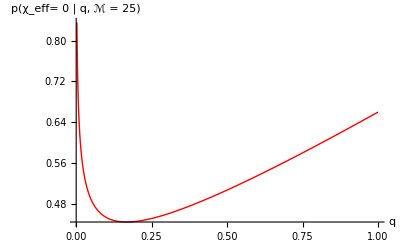

```mathematica
Plot[PChieffGivenqℳ / ℳ^2 ,{q, 0.001, 1.0}, AxesLabel-> {"q", "p(χ_eff= 0 | q, ℳ = 25)"}, LabelStyle->Directive[Bold, Medium], PlotStyle->{Red, Thick}]
```

```mathematica
Now using priors for q and ℳ, let's compute p(Subscript[χ, eff]) = 0
```

We define q to be uniform in [0.2, 1.0], and ℳ to be uniform in [25, 40]

```mathematica
Pq[q_] := 1/(1 - 0.2)
Pℳ[ℳ_] := 1.0/(40 - 25)
```

```mathematica
Integrate[Pq[q], {q, 0.2, 1}]
Integrate[Pℳ[ℳ], {ℳ, 25, 40}]
```

#### Integrate the p(χ_eff | q, ℳ) result

```mathematica
PChieffGivenq = Integrate[PChieffGivenqℳ, {ℳ, 25, 40}]
```

{{{(16125 (1+q)^(7/5) (4-2 Log[q]))/(4 q^(1/5))}}}

```mathematica
PChieff = Integrate[PChieffGivenq, {q, 0.2, 1}]
```

{{{35480.4}}}